```mathematica
ClearAll["Global`*"]
```

## Forces

```mathematica
m=1.99;
g=9.80655;
v0=0;
x0=0;
θ=Pi/4;
v[t_]:=v0+g t Tan[θ];
x[t_]:=x0+v0 t+1/2 g t^2 Tan[θ];
```

```mathematica
x[1]
```

4.90328

```mathematica
v[3]
x[3]
```

29.4196

44.1295

```mathematica
a[t_]:=g Tan[θ]
v[t_]=Integrate[a[t], t]
x[t_]=Integrate[v[t],t]
```

9.80655 t

4.90328 t^2

```mathematica
For[i=0,i≤100,i++,
Print[i];
Print[v[i]];
Print[x[i]];
]
```

0

0.

0.

1

9.80655

4.90328

2

19.6131

19.6131

3

29.4196

44.1295

4

39.2262

78.4524

5

49.0328

122.582

6

58.8393

176.518

7

68.6459

240.26

8

78.4524

313.81

9

88.259

397.165

10

98.0655

490.328

11

107.872

593.296

12

117.679

706.072

13

127.485

828.653

14

137.292

961.042

15

147.098

1103.24

16

156.905

1255.24

17

166.711

1417.05

18

176.518

1588.66

19

186.324

1770.08

20

196.131

1961.31

21

205.938

2162.34

22

215.744

2373.19

23

225.551

2593.83

24

235.357

2824.29

25

245.164

3064.55

26

254.97

3314.61

27

264.777

3574.49

28

274.583

3844.17

29

284.39

4123.65

30

294.197

4412.95

31

304.003

4712.05

32

313.81

5020.95

33

323.616

5339.67

34

333.423

5668.19

35

343.229

6006.51

36

353.036

6354.64

37

362.842

6712.58

38

372.649

7080.33

39

382.455

7457.88

40

392.262

7845.24

41

402.069

8242.41

42

411.875

8649.38

43

421.682

9066.16

44

431.488

9492.74

45

441.295

9929.13

46

451.101

10375.3

47

460.908

10831.3

48

470.714

11297.1

49

480.521

11772.8

50

490.328

12258.2

51

500.134

12753.4

52

509.941

13258.5

53

519.747

13773.3

54

529.554

14297.9

55

539.36

14832.4

56

549.167

15376.7

57

558.973

15930.7

58

568.78

16494.6

59

578.586

17068.3

60

588.393

17651.8

61

598.2

18245.1

62

608.006

18848.2

63

617.813

19461.1

64

627.619

20083.8

65

637.426

20716.3

66

647.232

21358.7

67

657.039

22010.8

68

666.845

22672.7

69

676.652

23344.5

70

686.459

24026.

71

696.265

24717.4

72

706.072

25418.6

73

715.878

26129.6

74

725.685

26850.3

75

735.491

27580.9

76

745.298

28321.3

77

755.104

29071.5

78

764.911

29831.5

79

774.717

30601.3

80

784.524

31381.

81

794.331

32170.4

82

804.137

32969.6

83

813.944

33778.7

84

823.75

34597.5

85

833.557

35426.2

86

843.363

36264.6

87

853.17

37112.9

88

862.976

37971.

89

872.783

38838.8

90

882.589

39716.5

91

892.396

40604.

92

902.203

41501.3

93

912.009

42408.4

94

921.816

43325.3

95

931.622

44252.1

96

941.429

45188.6

97

951.235

46134.9

98

961.042

47091.1

99

970.848

48057.

100

980.655

49032.8

## Matrices & Angles

```mathematica
ClearAll[α,β,γ,m,g]
yaw = {{Cos[α], -Sin[α], 0},
	{Sin[α], Cos[α], 0},
	{0,0,1}};
pitch={{Cos[β],0,Sin[β]},
	{0,1,0},
	{-Sin[β],0,Cos[β]}};
roll={{1,0,0},
	{0,Cos[γ],-Sin[γ]},
	{0,Sin[γ],Cos[γ]}};
totalrotation=yaw.pitch.roll;
MatrixForm[totalrotation]
```

(Cos[α] Cos[β] | -Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
Cos[β] Sin[α] | Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ] | Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]
-Sin[β] | Cos[β] Sin[γ] | Cos[β] Cos[γ])

```mathematica
(*g=9.80655;
m=.056+1.518;
α=0;
β=0;
γ=π/6;*)
u={0,0,1};
fhat=totalrotation.u;
N[fhat];
MatrixForm[N[totalrotation]];
fz=fhat[[3]]
magf=(m*g)/fz
f=magf*fhat
```

Cos[β] Cos[γ]

g m Sec[β] Sec[γ]

{g m Sec[β] Sec[γ] (Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]),g m Sec[β] Sec[γ] (Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]),g m}

### Solve the ODE

```mathematica
(*f=ma*)
fg={0,0,-m*g}
fnet=f+fg
a=fnet/m
t0=0;
dt=0.001;
v0={0,0,0};
x0={0,0,0};
```

{0,0,-g m}

{g m Sec[β] Sec[γ] (Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]),g m Sec[β] Sec[γ] (Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]),0}

{g Sec[β] Sec[γ] (Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]),g Sec[β] Sec[γ] (Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]),0}

```mathematica
v=v0+a*dt
x=x0+v*dt
```

{0.001 g Sec[β] Sec[γ] (Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]),0.001 g Sec[β] Sec[γ] (Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]),0.}

{1.×10^-6 g Sec[β] Sec[γ] (Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]),1.×10^-6 g Sec[β] Sec[γ] (Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]),0.}

```mathematica
thing[α_,β_,γ_]:={g*m*Sec[β]*Sec[γ]*(Cos[α]*Cos[γ]*Sin[β]+Sin[α]*Sin[γ]),g*m*Sec[β]*Sec[γ]*(Cos[γ]*Sin[α]*Sin[β]-Cos[α]*Sin[γ]),0}/m
α=0;
β=0;
γ=π/6;
g=9.80655;
m=.056+1.518;
t0=0;
tf=1.0;
dt=0.01;
v0={0,0,0};
r0={0,0,0};
v=v0;
r=r0;
vt={{0,v0}};
rt={{0,r0}};
vyt={{0,v0[[2]]}};
yt={{0,r0[[2]]}};
For[t=dt,t<=tf,t=t+dt,
vn=v+thing[α,β,γ]*dt;
rn=r+v*dt;
v=vn;
r=rn;
AppendTo[vt,{t,v}];
AppendTo[rt,{t,r}];
AppendTo[vyt,{t,v[[2]]}];
AppendTo[yt,{t,r[[2]]}]]
```

0 |   0
  0
  0
 0.0 |  0.0
 0.0
 0.0
 0.0 |  0.0
-0.0
 0.0
 0.0 |  0.0
-0.0
 0.0
 0.0 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.0
 0.0
 0.1 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.1
 0.0
 0.2 |  0.0
-0.2
 0.0
 0.3 |  0.0
-0.2
 0.0
 0.3 |  0.0
-0.2
 0.0
 0.3 |  0.0
-0.2
 0.0
 0.3 |  0.0
-0.2
 0.0
 0.3 |  0.0
-0.2
 0.0
 0.3 |  0.0
-0.2
 0.0
 0.3 |  0.0
-0.3
 0.0
 0.3 |  0.0
-0.3
 0.0
 0.3 |  0.0
-0.3
 0.0
 0.3 |  0.0
-0.3
 0.0
 0.4 |  0.0
-0.3
 0.0
 0.4 |  0.0
-0.4
 0.0
 0.4 |  0.0
-0.4
 0.0
 0.4 |  0.0
-0.4
 0.0
 0.4 |  0.0
-0.4
 0.0
 0.4 |  0.0
-0.4
 0.0
 0.4 |  0.0
-0.5
 0.0
 0.4 |  0.0
-0.5
 0.0
 0.4 |  0.0
-0.5
 0.0
 0.4 |  0.0
-0.5
 0.0
 0.5 |  0.0
-0.6
 0.0
 0.5 |  0.0
-0.6
 0.0
 0.5 |  0.0
-0.6
 0.0
 0.5 |  0.0
-0.6
 0.0
 0.5 |  0.0
-0.7
 0.0
 0.5 |  0.0
-0.7
 0.0
 0.5 |  0.0
-0.7
 0.0
 0.5 |  0.0
-0.8
 0.0
 0.5 |  0.0
-0.8
 0.0
 0.5 |  0.0
-0.8
 0.0
 0.6 |  0.0
-0.8
 0.0
 0.6 |  0.0
-0.9
 0.0
 0.6 |  0.0
-0.9
 0.0
 0.6 |  0.0
-0.9
 0.0
 0.6 |  0.0
-1.0
 0.0
 0.6 |  0.0
-1.0
 0.0
 0.6 |  0.0
-1.0
 0.0
 0.6 |  0.0
-1.1
 0.0
 0.6 |  0.0
-1.1
 0.0
 0.6 |  0.0
-1.1
 0.0
 0.7 |  0.0
-1.2
 0.0
 0.7 |  0.0
-1.2
 0.0
 0.7 |  0.0
-1.3
 0.0
 0.7 |  0.0
-1.3
 0.0
 0.7 |  0.0
-1.3
 0.0
 0.7 |  0.0
-1.4
 0.0
 0.7 |  0.0
-1.4
 0.0
 0.7 |  0.0
-1.4
 0.0
 0.7 |  0.0
-1.5
 0.0
 0.7 |  0.0
-1.5
 0.0
 0.8 |  0.0
-1.6
 0.0
 0.8 |  0.0
-1.6
 0.0
 0.8 |  0.0
-1.7
 0.0
 0.8 |  0.0
-1.7
 0.0
 0.8 |  0.0
-1.7
 0.0
 0.8 |  0.0
-1.8
 0.0
 0.8 |  0.0
-1.8
 0.0
 0.8 |  0.0
-1.9
 0.0
 0.8 |  0.0
-1.9
 0.0
 0.8 |  0.0
-2.0
 0.0
 0.9 |  0.0
-2.0
 0.0
 0.9 |  0.0
-2.1
 0.0
 0.9 |  0.0
-2.1
 0.0
 0.9 |  0.0
-2.2
 0.0
 0.9 |  0.0
-2.2
 0.0
 0.9 |  0.0
-2.3
 0.0
 0.9 |  0.0
-2.3
 0.0
 0.9 |  0.0
-2.4
 0.0
 0.9 |  0.0
-2.4
 0.0
 0.9 |  0.0
-2.5
 0.0
 1.0 |  0.0
-2.5
 0.0
 1.0 |  0.0
-2.6
 0.0
 1.0 |  0.0
-2.6
 0.0
 1.0 |  0.0
-2.7
 0.0
 1.0 |  0.0
-2.7
 0.0
 1.0 |  0.0
-2.8
 0.0

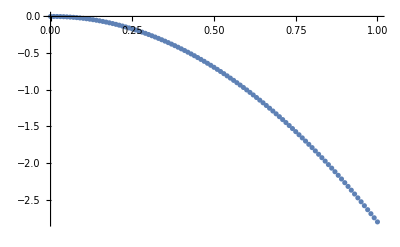

```mathematica
PaddedForm[TableForm[rt],{2,1}]
ListPlot[yt]
```

```mathematica
integration=Integrate[thing[α,β,γ],s,s];
Plot[integration,{s,t0,tf}];
integration[tf]
rt[[tf]]
```

{0,-2.83091 s^2,0}[1.]

{0,{0,0,0}}